# Learning to recognize different works of literature

```mathematica
labels={"AliceInWonderland","BeowulfModern","DonQuixoteIEnglish","Hamlet","OriginOfSpecies"}
```

{AliceInWonderland,BeowulfModern,DonQuixoteIEnglish,Hamlet,OriginOfSpecies}

```mathematica
texts=Map[{"Text",#}&,labels]
```

{{Text,AliceInWonderland},{Text,BeowulfModern},{Text,DonQuixoteIEnglish},{Text,Hamlet},{Text,OriginOfSpecies}}

```mathematica
rawdata=RandomSample[
Flatten[
Map[
Function[{text},
Map[#->Last[text]&,
RandomSample[TextSentences[ExampleData[text]],400]]],
texts]]];
```

```mathematica
rawdata//Length
```

2000

```mathematica
dictionary=Union[Flatten[Map[TextWords[First[#]]&,rawdata]]];
```

```mathematica
Length[dictionary]
```

8123

```mathematica
rawdata[[20]]
```

On Rocinante oft a weary ride.→DonQuixoteIEnglish

```mathematica
TextEncoder[string_]:=Module[{vector,positions},vector=ConstantArray[0,Length[dictionary]];
positions=Flatten[Position[dictionary,#]&/@TextWords[string]];
vector[[positions]]=1;
vector]
```

```mathematica
data=Map[TextEncoder[First[#]]->Last[#]&,rawdata];
```

```mathematica
Length[data]
```

2000

```mathematica
training=data[[1;;1800]];
validation=data[[1801;;2000]];
```

```mathematica
Length[training]
```

1800

```mathematica
Length[validation]
```

200

```mathematica
net=NetChain[{
DotPlusLayer[1000],
ElementwiseLayer[Ramp],
DotPlusLayer[5],
ElementwiseLayer[Ramp],
SoftmaxLayer[]
},
"Input"->Length[dictionary],
"Output"->NetDecoder[{"Class",labels}]
]
```

NetChain[]

```mathematica
net=NetInitialize[net]
```

NetChain[]

```mathematica
NetGraph[net]
```

NetGraph[]

```mathematica
net=NetTrain[net,training,
ValidationSet->validation,
TargetDevice->"GPU",
MaxTrainingRounds->10000
]
```

NetChain[]

```mathematica
RandomSample[rawdata,3]
```

{- O good Horatio, what a wounded name, Things standing thus unknown, shall live behind me!→Hamlet,So then, provided it seems good to you, Master Nicholas, I say let this and 'Amadis of Gaul' be remitted the penalty of fire, and as for all the rest, let them perish without further question or query."→DonQuixoteIEnglish,"Because just now thou smellest stronger than ever, and not of ambergris," answered Don Quixote.→DonQuixoteIEnglish}

```mathematica
net[TextEncoder["- O good Horatio, what a wounded name, Things standing thus unknown, shall live behind me!"]]
```

Hamlet

```mathematica
validation//Length
```

200

```mathematica
cm=ClassifierMeasurements[net,validation]
```

ClassifierMeasurementsObject[…]

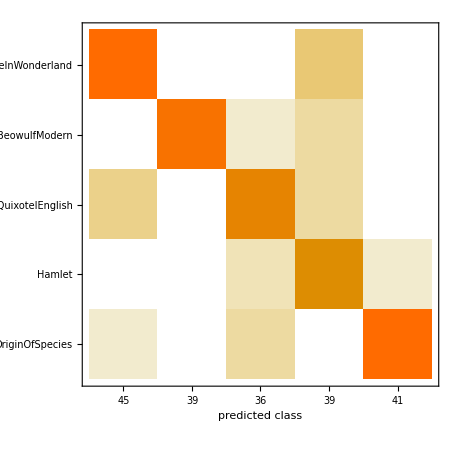

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
cm["Accuracy"]
```

0.885

```mathematica
cm=ClassifierMeasurements[net,validation]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["ConfusionMatrixPlot"]
```